```mathematica
(*Problem 4*)
```

```mathematica
KE = (1/2)*(m1+m2)*(D[xCOM[t],t]^2+D[yCOM[t],t]^2)+(1/2)*(m1*m2)*(D[r[t],t]^2+r[t]^2*D[θ[t],t]^2)/(m1+m2);
```

```mathematica
PE=(k/2)*(r[t]-b)^2;
```

```mathematica
L=KE-PE;
```

```mathematica
(*Lagrangian*)
```

```mathematica
L//FullSimplify
```

1/2 (-k (b-r[t])^2+(m1+m2) (xCOM'[t]^2+yCOM'[t]^2)+(m1 m2 (r'[t]^2+r[t]^2 θ'[t]^2))/(m1+m2))

```mathematica
1/2 (-k (b-r[t])^2+(m1+m2) (xCOM'[t]^2+yCOM'[t]^2)+(m1 m2 (r'[t]^2+r[t]^2 θ'[t]^2))/(m1+m2))//TeXForm
```

\frac{1}{2} \left(-k (b-r(t))^2+\frac{\text{m1} \text{m2} \left(r'(t)^2+r(t)^2 \theta
   '(t)^2\right)}{\text{m1}+\text{m2}}+(\text{m1}+\text{m2}) \left(\text{xCOM}'(t)^2+\text{yCOM}'(t)^2\right)\right)

```mathematica
(*Lagrangian EOMs*)
```

```mathematica
(*xCOM equation*)
```

```mathematica
Solve[FullSimplify[D[D[L,xCOM'[t]],t]==D[L,xCOM[t]]],xCOM''[t]][[1]]//Expand
```

{xCOM''[t]→0}

```mathematica
(*yCOM equation*)
```

```mathematica
Solve[FullSimplify[D[D[L,yCOM'[t]],t]==D[L,yCOM[t]]],yCOM''[t]][[1]]//Expand
```

{yCOM''[t]→0}

```mathematica
(*r equation*)
```

```mathematica
Solve[FullSimplify[D[D[L,r'[t]],t]==D[L,r[t]]],r''[t]][[1]]//FullSimplify
```

{r''[t]→(k (m1+m2) (b-r[t]))/(m1 m2)+r[t] θ'[t]^2}

```mathematica
(*theta equation*)
```

```mathematica
Solve[FullSimplify[D[D[L,θ'[t]],t]==D[L,θ[t]]],θ''[t]][[1]]//Expand
```

{θ''[t]→-(2 r'[t] θ'[t])/r[t]}

```mathematica
(*Cyclic coordinates*)
```

```mathematica
D[L,xCOM[t]]
```

0

```mathematica
D[L,yCOM[t]]
```

0

```mathematica
D[L,θ[t]]
```

0

```mathematica
(*Conserved generalized momenta*)
```

```mathematica
D[L,xCOM'[t]]//Simplify
```

(m1+m2) xCOM'[t]

```mathematica
D[L,yCOM'[t]]//Simplify
```

(m1+m2) yCOM'[t]

```mathematica
D[L,θ'[t]]//Simplify
```

(m1 m2 r[t]^2 θ'[t])/(m1+m2)

```mathematica
Solve[(1/2)*k*(b-r)^2==(1/2)*μ*r^2*θ'^2,r]//FullSimplify
```

{{r→(b √k)/(√k+√μ θ')},{r→(b √k)/(√k-√μ θ')}}

```mathematica
V[r_] = (1/2)*k*(b-r)^2-(1/2)*μ*r^2*θ'^2;
```

```mathematica
D[V[r],r]
```

-k (b-r)-r μ (θ')^2

```mathematica
Solve[D[V[r],r]==0,r]
```

{{r→(b k)/(k-μ (θ')^2)}}

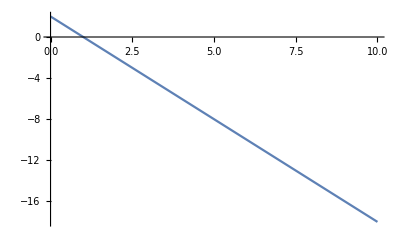

```mathematica
Plot[(1/2)*1*(2-r)^2-(1/2)*1*r^2*1^2,{r,0,10}]
```